```mathematica
(*This notebook is used to generate figure 4 (a),(f), and (k) in the article
"Analysis of Neural Activation in Time-dependent Membrane Capacitance Models" by 
Courdurier M. , Medina L. E. and Paduro E.*)
SetDirectory[NotebookDirectory[]];
threshold = 1;
case=3;
Switch[case,
1,T=100;C0=1;filename="Fig4a.eps";
pointList={{{0.17,0.3}},{{0.25,0.3}},{{0.17,0.7}},{{0.25,0.7}}};,
2,T=30;C0=1;filename="Fig4f.eps";
pointList={{{0.17,0.3}},{{0.25,0.3}},{{0.17,0.7}},{{0.25,0.7}}};,
3,T=4;C0=1;filename="Fig4k.eps";
pointList={{{0.17,0.3}},{{0.25,0.3}},{{0.17,0.7}},{{0.25,0.7}}};
]
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=1000;
(*Equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

```mathematica
(*Simulation*)
simulation={};
κ2=0.5;κ4=1;
Do[Do[
κ1=0.2+δ;κ3=0.7+δ;
Ct[t_]=Which[Mod[t,T]<κ1 T,C0,Mod[t,T]<κ2 T,C0+(Mod[t,T]-κ1 T)(C1-C0)/(κ2 T- κ1 T), Mod[t,T]<κ3 T,C1, True,C1+(Mod[t,T]-κ3 T)(C0-C1)/(T- κ3 T)];
{U,W}=NDSolveValue[{u'[t] ==u[t]/Ct[t]-u[t]^3/(3Ct[t]^3)-w[t],w'[t]==ep(u[t]/Ct[t]-γ w[t] + β),u[0]==v0 Ct[0],w[0]==w0},{u,w},{t,0,maxtime}];
peaks = FindPeaks[Table[U[t]/Ct[t],{t,0,maxtime,1}],2,0,threshold];
count=Length[peaks];
point = {δ,C0 - C1,count/maxtime *1000};
simulation = Append[simulation,point];
,{δ,0,0.299,0.02}],{C1,0.2,0.96,0.05}];
```

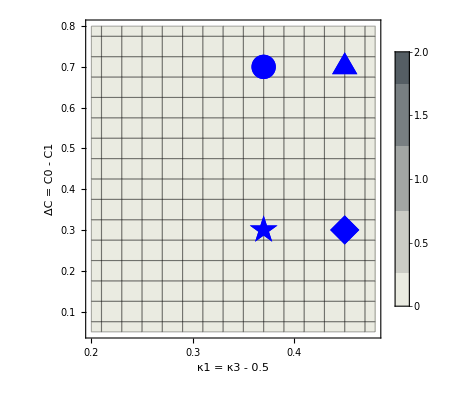

Fig4k.eps

```mathematica
(*Visualization*)
x1range={0.2,0.5};
x2range={0.7,1};
referencerange={0,0.3};
referenceticks=FindDivisions[Append[referencerange,0.05],7];
x1ticks=Quiet@Transpose@{referenceticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[referenceticks,referencerange,x1range]};
x2ticks=Quiet@Transpose@{referenceticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[referenceticks,referencerange,x2range]};

extract=simulation[[All,{1,2,3}]];
extract=extract.{{1,0,0},{0,1,0},{0,0,T/1000}};
g1= ListDensityPlot[extract,
Mesh->All,
InterpolationOrder->0,
PlotLegends->BarLegend[{Automatic,{0,2}}],
ColorFunction->(ColorData["GrayTones"][1-0.6*Round[2*#]/4]&),
ColorFunctionScaling->False,
PlotLegends->Automatic,
FrameLabel->{{"ΔC = C0 - C1",Automatic},{"κ1 = κ3 - 0.5",None}},
PlotRange->{Full,Full,{0,2}},
PlotRangeClipping->False,
LabelStyle->Directive[Black,FontSize->20],
FrameTicks->{{Automatic,Automatic},{x1ticks,Automatic}}
];
g2=ListPlot[pointList,
PlotMarkers->{
Style["★",Blue,30],
Style["◆",Blue,30],
Style["●",Blue,25],
Style["▲",Blue,30]}];
g3=Show[g1,g2]
Export[filename,g3]
```